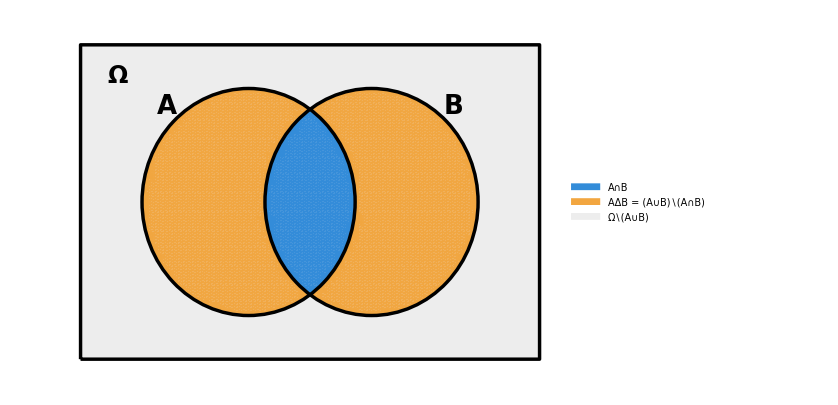

```mathematica
r=1.3;sep=0.75;
limX=2.8;limY=1.8;

colorOmega=RGBColor[0.93,0.93,0.93];  (*Ω\ (A∪B)*)
colorSim=RGBColor[0.95,0.65,0.25];    (*A Δ B*)
colorInter=RGBColor[0.2,0.55,0.85];   (*A ∩ B*)

grafico=Show[Graphics[{colorOmega,Rectangle[{-limX,-limY},{limX,limY}]}],RegionPlot[((x+sep)^2+y^2<r^2&&!((x-sep)^2+y^2<r^2))||((x-sep)^2+y^2<r^2&&!((x+sep)^2+y^2<r^2)),{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[colorSim,Opacity[0.85]],BoundaryStyle->None,PlotPoints->100,MaxRecursion->3],RegionPlot[(x+sep)^2+y^2<r^2&&(x-sep)^2+y^2<r^2,{x,-limX,limX},{y,-limY,limY},PlotStyle->Directive[colorInter,Opacity[0.9]],BoundaryStyle->None,PlotPoints->100,MaxRecursion->3],Graphics[{FaceForm[None],EdgeForm[{Black,Thickness[0.004]}],Rectangle[{-limX,-limY},{limX,limY}],Black,Thickness[0.004],Circle[{-sep,0},r],Circle[{sep,0},r],Text[Style["A",26,Bold],{-sep-r+0.3,r-0.2}],Text[Style["B",26,Bold],{sep+r-0.3,r-0.2}],Text[Style["Ω",24,Bold],{-limX+0.45,limY-0.35}]}],PlotRange->{{-limX-0.1,limX+0.1},{-limY-0.1,limY+0.1}},AspectRatio->Automatic,ImageSize->620];

imagenFinal=Legended[grafico,SwatchLegend[{colorInter,colorSim,colorOmega},{"A∩B","AΔB = (A∪B)∖(A∩B)","Ω∖(A∪B)"},LabelStyle->Directive[FontSize->20],LegendMarkerSize->25]];

imagenFinal
```

```mathematica
Export["prob_quesada_2_2_a.png",imagenFinal,Background->None,ImageResolution->1200];
```

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["prob_quesada_2_2_a.png"]]]
```